```mathematica
Plot3D[Exp[-(x^2+y^2)/2]/(2 Pi),{x,-3,3},{y,-3,3},PlotRange->All,AxesLabel->{Style["x", FontSize->30, FontColor->Black],Style["ρ", FontSize->30, FontColor->Black],Style["H(x,ρ)", FontSize-> 30, FontColor->Black ]},PlotLabel->Style["Hamiltonian", FontSize->30, FontColor->Black], PlotPoints->1000, ColorFunction->"Rainbow", MaxRecursion->4]
```

-Graphics3D-

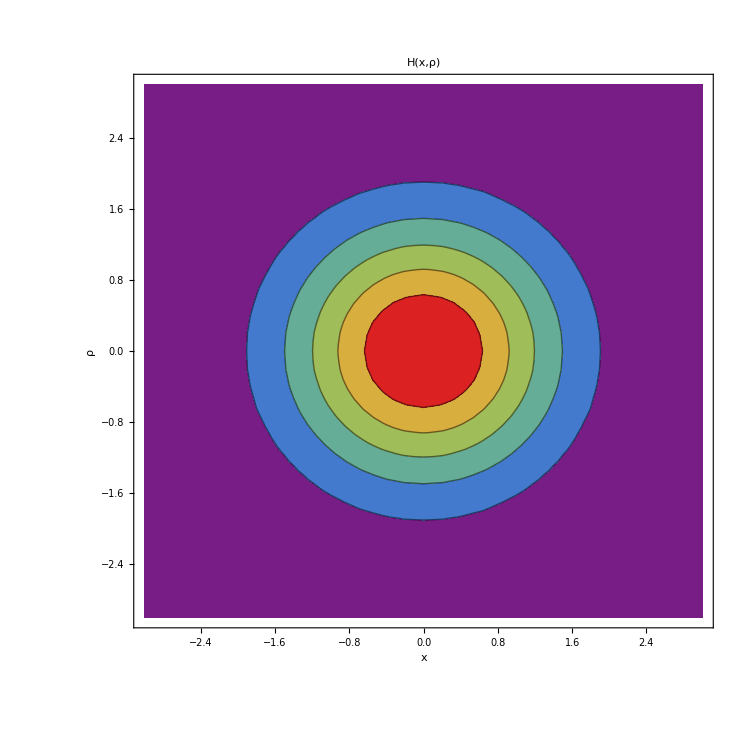

```mathematica
ContourPlot[Exp[-(x^2+y^2)/2]/(2 Pi),{x,-3,3},{y,-3,3},Contours->5,FrameLabel->{Style["x", FontSize->30, FontColor->Black],Style["ρ", FontSize->30, FontColor->Black]}, ColorFunction->"Rainbow", PlotLabel->Style["H(x,ρ)", FontSize-> 30, FontColor->Black ]]
```

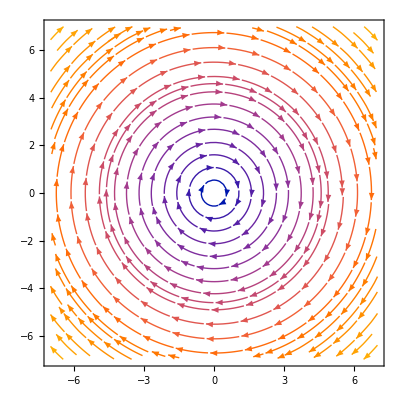

```mathematica
StreamPlot[{2*y, -2*x},{x,-7,7},{y,-7,7},StreamStyle->Directive[Opacity[1]],StreamPoints->Fine,StreamScale->0.1, ColorFunction->"Rainbow"]
```

```mathematica
fX = E^(-1/2*(x-1)^2)+E^(-1/2/(2^2)*(x-4)^2)
```

ⅇ^(-1/8 (-4+x)^2)+ⅇ^(-1/2 (-1+x)^2)

```mathematica
NIntegrate[fX,{x, -Infinity, Infinity}]
```

7.51988

```mathematica
NIntegrate[ E^(-1/2*(x-1)^2), {x, -Infinity, Infinity}]
```

2.50663

```mathematica
f = 0.1* E^(-1/2/(1^2)*((x+5)^2))+0.5*E^(-1/2/(1^2)*((x)^2))+0.2*E^(-1/2/(1^2)*((x-5)^2))+0.2*E^(-1/2/(1^2)*((x+10)^2))+0.1*E^(-1/2/(1^2)*((x-10)^2))
```

0.1 ⅇ^(-1/2 (-10+x)^2)+0.2 ⅇ^(-1/2 (-5+x)^2)+0.5 ⅇ^(-x^2/2)+0.1 ⅇ^(-1/2 (5+x)^2)+0.2 ⅇ^(-1/2 (10+x)^2)

```mathematica
NC = NIntegrate[f, {x, -Infinity, Infinity}]
```

2.75729

```mathematica
Expectation = NIntegrate[x*f/NC, {x, -Infinity, Infinity}]
```

Set::wrsym: Symbol Expectation is Protected.

-0.454545